```mathematica
SetDirectory@NotebookDirectory[]
```

/media/Storage/Coding/Blog/mathematica

```mathematica
r=0.9;
square[{a_,b_,c_,d_}]:=Graphics[{Line[{{1,1},{1,-1},{-1,-1},{-1,1},{1,1}}],Inset[Style[First@#,Large],Last@#]&/@{{a,{-r,r}},{b,{r,r}},{c,{r,-r}},{d,{-r,-r}}}},PlotRange->All]
```

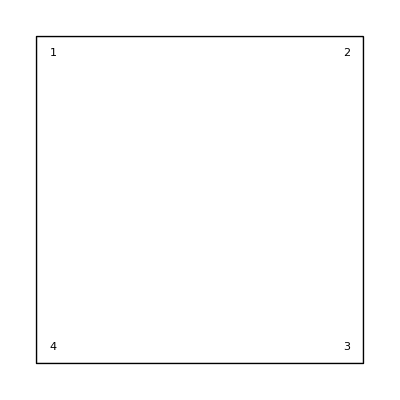

```mathematica
square@{1,2,3,4}
```

```mathematica
rot[{a_,b_,c_,d_}]:={b,c,d,a}
```

```mathematica
nop={1,2,3,4}
```

{1,2,3,4}

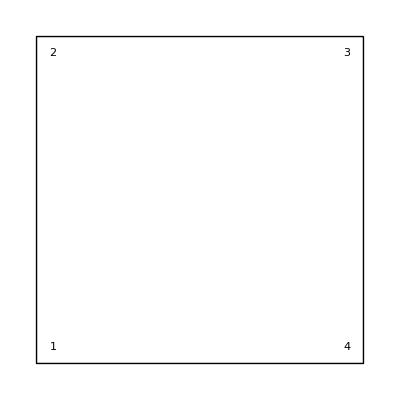

```mathematica
square@rot@nop
```

```mathematica
refl[{a_,b_,c_,d_}]:={a,d,c,b}
```

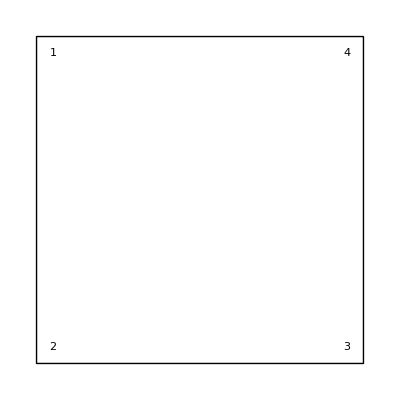

```mathematica
square@refl@nop
```

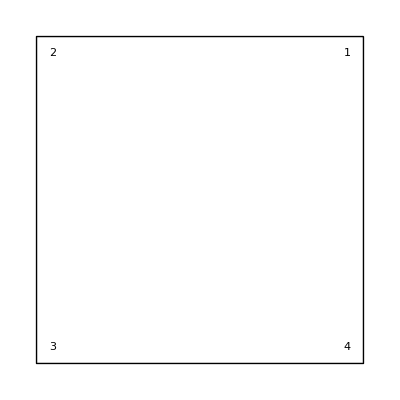

```mathematica
square@refl@rot@nop
```

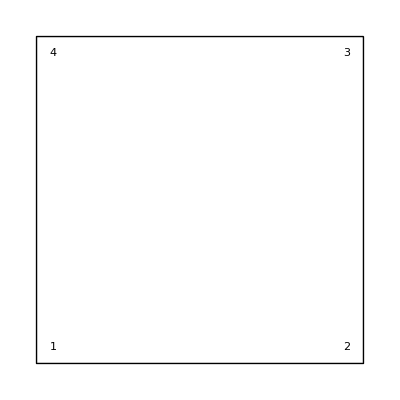

```mathematica
square@rot@refl@nop
```